## Pristine ZrC electron transport;

```mathematica
Some basic information;
```

```mathematica
alatts={4.575,4.600,4.625,4.6583,4.685,4.730,4.759,4.801,4.850};
tempps={0,10,300,500,760,1000,1500,1900,2500,3200,3800};
temppps=tempps[[2;;11]];
temps2={300,300,760,1900,2500,3200,3800};
temps3={300,760,1900,2500,3200,3800};
temps4={10,300,760,1900,2500,3200,3800};
THz2meV=1/4.135665538536;K2meV=0.086173324;kjmol2evatom=1/(96.487*64);
Nat=64;Natvac=63;mass={91.224,12.0107,1};
ang2bohr=1/0.529177208;ev2har=1/27.211396;kB=1000*8.617332478*10^−5;
eVperAng2harperbohr=ev2har/ang2bohr;eVperAng22harperbohr2=ev2har/ang2bohr/ang2bohr;
HarBohr=meVperAng22harperbohr2=0.001*ev2har/ang2bohr/ang2bohr;
(*Constant, Fermi-Dirac and Fermi-Dirac changing with energy*)
K2eV=8.617332478*10^−5;
fermiDirac[energy_,temp_]:=1/(Exp[energy/(K2eV*temp)]+1)
(*define sigma and8 kappa kernels*)
(*temp in energy units*)
sigmaK[energy_,temp_]:=-D[fermiDirac[energy,temp],energy]
kappaK[energy_,temp_]:=-(1/temp)*(energy^2)*D[fermiDirac[energy,temp],energy]
eV2ryd=1/13.605698066;ryd2eV=13.605698066;
```

```mathematica
Import data;
SetDirectory["/Volumes/MicroSD/Dropbox/EPW/ZrC/LDA/"];
temps={"0K","10K","300K","500K","760K","1000K","1500K","1900K","2500K","3200K","3800K"};
scatteringRates=Table[ReadList[StringJoin["Variable_Volume/ScatteringRates/constant_smearing/kRandom/",ToString@temps[[i]],"/scattering_rate",ToString@temps[[i]]],{Number, Number,Number, Number,Number}],{i,1,11}];
```

#### List of energy vs rate or lifetime;

```mathematica
rateData=Table[Transpose[{Transpose[scatteringRates[[i]]][[3]],Transpose[scatteringRates[[i]]][[4]]}],{i,1,11}];
lifeData=Table[Transpose[{Transpose[scatteringRates[[i]]][[3]],Transpose[1/scatteringRates[[i]]][[4]]}],{i,1,11}];
```

```mathematica
rateData[[1]][[2]][[2]]
1/lifeData[[1]][[2]][[2]]
```

2.09387×10^14

2.09387×10^14

```mathematica
rateData[[1]][[200]][[2]]
1/lifeData[[1]][[200]][[2]]
```

3.56642×10^14

3.56642×10^14

```mathematica
Plot rate R and lifetime τ ;
```

```mathematica
ListPlot[rateData[[1]],PlotRange->{All,{0,6*10^14}}]
ListPlot[lifeData[[1]],PlotRange->{All,{0,10^-9}}]
```

-Graphics-

-Graphics-

#### Randomly sample rate and life τ;

```mathematica
rateDataR6=Table[RandomSample[rateData[[i]],0.15*10^6],{i,1,11}];
rateDataR5=Table[RandomSample[rateData[[i]],10^5],{i,1,11}];
rateDataR4=Table[RandomSample[rateData[[i]],10^4],{i,1,11}];
rateDataR3=Table[RandomSample[rateData[[i]],10^3],{i,1,11}];
rateDataR2=Table[RandomSample[rateData[[i]],10^2],{i,1,11}];
```

```mathematica
lifeDataR6=Table[RandomSample[lifeData[[i]],0.15*10^6],{i,1,11}];
lifeDataR5=Table[RandomSample[lifeData[[i]],10^5],{i,1,11}];
lifeDataR4=Table[RandomSample[lifeData[[i]],10^4],{i,1,11}];
lifeDataR3=Table[RandomSample[lifeData[[i]],10^3],{i,1,11}];
lifeDataR2=Table[RandomSample[lifeData[[i]],10^2],{i,1,11}];
```

```mathematica
ListPlot[Table[rateData[[i]],{i,2,11,2}],PlotLegends->SwatchLegend[Table[temps[[i]],{i,2,11,2}]],Frame->True,FrameLabel->{"E-E_F(eV)","Scattering rate (1/s)"},PlotRange->{All,{0,6*10^15}}]
```

-Graphics-

```mathematica
ListPlot[Table[rateDataR5[[i]],{i,2,11,2}],PlotLegends->SwatchLegend[Table[temps[[i]],{i,2,11,2}]],Frame->True,FrameLabel->{"E-E_F(eV)","Scattering rate (1/s)"},PlotRange->{All,{0,6*10^15}}]
```

-Graphics-

```mathematica
ListPlot[Table[lifeDataR5[[i]],{i,2,11,2}],PlotLegends->SwatchLegend[Table[temps[[i]],{i,2,11,2}]],Frame->True,FrameLabel->{"E-E_F(eV)","Lifetime tau (s)"},PlotRange->{{-5,5},{0,5*10^-14}}]
```

-Graphics-

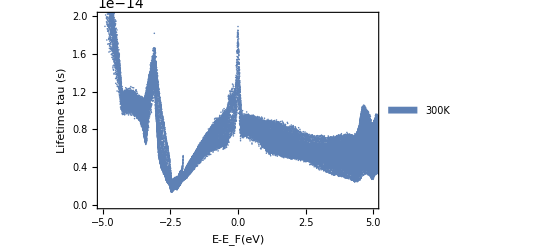

```mathematica
ListPlot[Table[lifeDataR5[[i]],{i,3,3,1}],PlotLegends->SwatchLegend[Table[temps[[i]],{i,3,3,1}]],Frame->True,FrameLabel->{"E-E_F(eV)","Lifetime tau (s)"},PlotRange->{{-5,5},{0,2*10^-14}}]
```

#### Lifetime data and moving mean;

```mathematica
(*Show[Table[{ListPlot[rateDataR5[[i]],PlotRange->{All,{0,6*10^15}},Frame->True,FrameLabel->{"E-E_F(eV)","Scattering rate (s)"},ImageSize->600],ListPlot[MovingMap[Mean,{rateDataR5[[i]]},0.11],PlotStyle->Red]},{i,1,11,3}]]*)
```

-Graphics-

```mathematica
Gaussian process model;
```

```mathematica
(*rateDataR4GP=Flatten[{#1->#2}&@@@rateDataR4[[1]]];
p4=Predict[rateDataR4GP,Method->"GaussianProcess"];*)
```

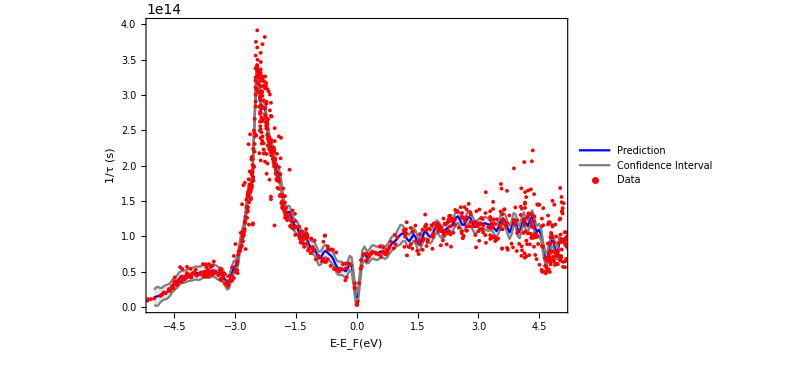

```mathematica
(*Show[Plot[{p4[x],p4[x]+StandardDeviation[p4[x,"Distribution"]],p4[x]-StandardDeviation[p4[x,"Distribution"]]},{x,-5,5},PlotStyle->{Blue,Gray,Gray},Filling->{2->{3}},Exclusions->False,PerformanceGoal->"Speed",PlotLegends->{"Prediction","Confidence Interval"},Frame->True,FrameLabel->{"E-E_F(eV)","1/τ (s)"},ImageSize->600,PlotRange->{{-5,5},{0,4*10^14}}],ListPlot[List@@@rateDataR4GP,PlotStyle->Red,PlotLegends->{"Data"}]]*)
```

```mathematica
Interpolate tau in energy;
```

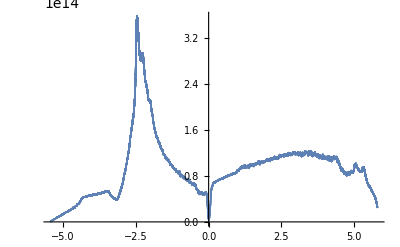

```mathematica
ListPlot@Interpolation[MovingMap[Mean,{rateDataR5[[1]]},0.02],InterpolationOrder->1,Method->"Hermite"]
```

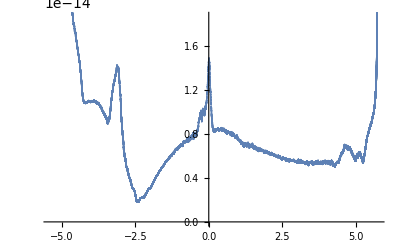

```mathematica
ListPlot@Interpolation[MovingMap[Mean,{lifeDataR5[[3]]},0.02],InterpolationOrder->1,Method->"Hermite"]
```

```mathematica
interRate=Table[Interpolation[MovingMap[Mean,{rateDataR5[[i]]},0.02],InterpolationOrder->1,Method->"Hermite"],{i,1,11}];
```

```mathematica
interTau=Table[Interpolation[MovingMap[Mean,{lifeDataR5[[i]]},0.02],InterpolationOrder->1,Method->"Hermite"],{i,1,11}];
```

```mathematica
interRate[[1]][4]
1/(interTau[[1]][4])
```

1.11806×10^14

1.04943×10^14

```mathematica
Plot rate and 1/tau;
```

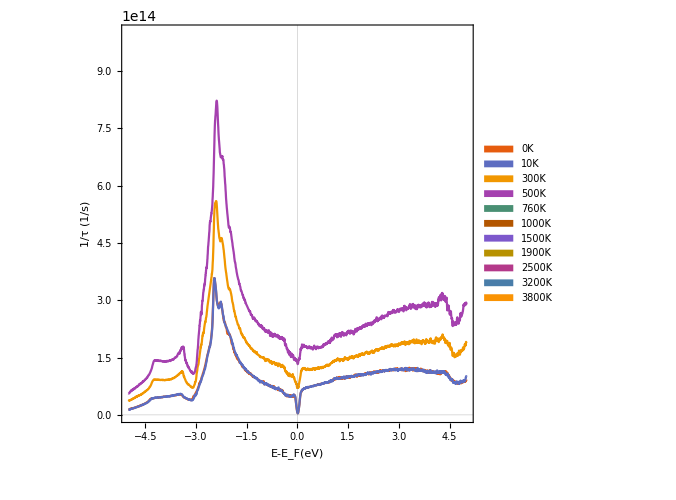

```mathematica
Plot[Evaluate@Table[interRate[[i]][x],{i,1,11}],{x,-5,5},PlotLegends->SwatchLegend[temps],FrameTicksStyle->15,Frame->True,AspectRatio->1,FrameLabel->{Style["E-E_F(eV)",15],Style["1/τ (1/s)",15]},PlotTheme->"Scientific",ImageSize->500,PlotRange->{All,{0,8*10^15}}]
```

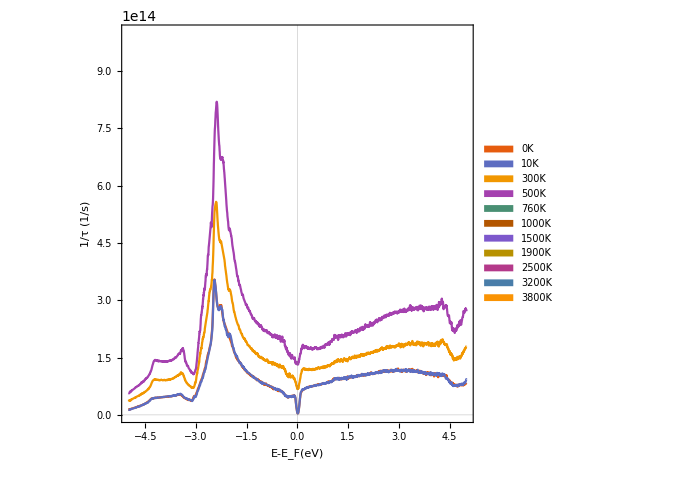

```mathematica
Plot[Evaluate@Table[1/interTau[[i]][x],{i,1,11}],{x,-5,5},PlotLegends->SwatchLegend[temps],FrameTicksStyle->15,Frame->True,AspectRatio->1,FrameLabel->{Style["E-E_F(eV)",15],Style["1/τ (1/s)",15]},PlotTheme->"Scientific",ImageSize->500]
```

```mathematica
Plot tau and 1/rate;
```

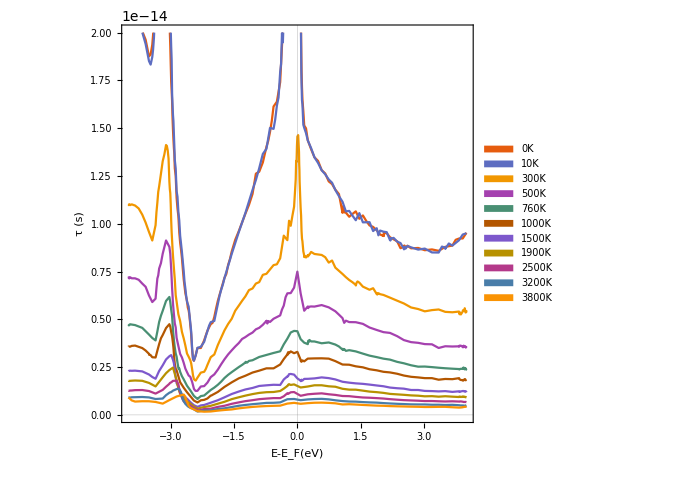

```mathematica
Plot[Evaluate@Table[interTau[[i]][x],{i,1,11}],{x,-4,4},PlotRange->{{-4,4},{0,2*10^-14}},PlotLegends->SwatchLegend[temps],FrameTicksStyle->15,Frame->True,AspectRatio->1,FrameLabel->{Style["E-E_F(eV)",15],Style["τ (s)",15]},PlotTheme->"Scientific",PlotRange->All,ImageSize->500]
```

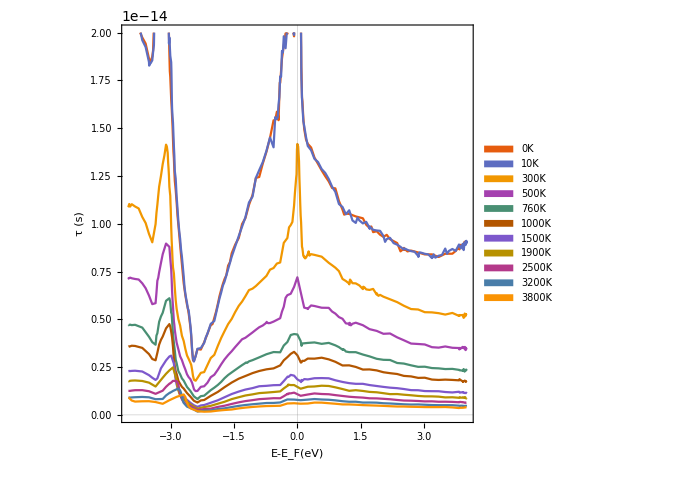

```mathematica
Plot[Evaluate@Table[1/interRate[[i]][x],{i,1,11}],{x,-4,4},PlotRange->{{-4,4},{0,2*10^-14}},PlotLegends->SwatchLegend[temps],FrameTicksStyle->15,Frame->True,AspectRatio->1,FrameLabel->{Style["E-E_F(eV)",15],Style["τ (s)",15]},PlotTheme->"Scientific",PlotRange->All,ImageSize->500]
```

```mathematica
Plot Rate times the charge transport distribution function;
```

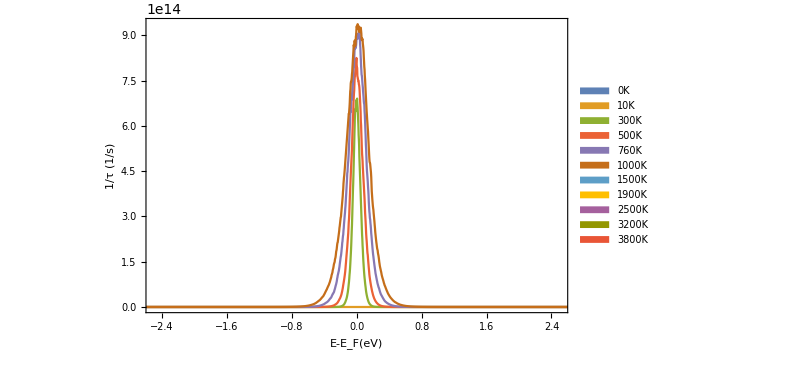

```mathematica
Plot[Evaluate@Table[Evaluate[sigmaK[x,tempps[[i]]]*interRate[[i]][x]],{i,1,11}],{x,-5,5},PlotLegends->SwatchLegend[temps],Frame->True,FrameLabel->{"E-E_F(eV)","1/τ (1/s)"},ImageSize->600,PlotRange->{{-2.5,2.5},All}]
Off[s::Part::pkspec1]
Off[s::Power::infy]
Off[s::Infinity::indet]
```

```mathematica
Plot tau times the charge transport distribution function;
```

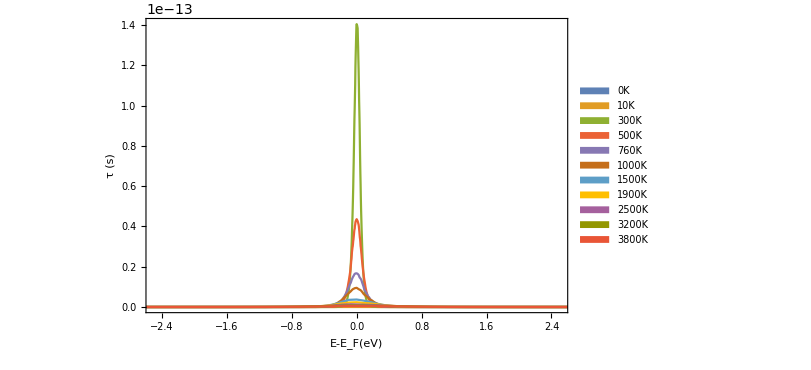

```mathematica
Plot[Evaluate@Table[Evaluate[sigmaK[x,tempps[[i]]]*interTau[[i]][x]],{i,1,11}],{x,-5,5},PlotLegends->SwatchLegend[temps],Frame->True,FrameLabel->{"E-E_F(eV)","τ (s)"},ImageSize->600,PlotRange->{{-2.5,2.5},All}]
Off[s::Infinity::indet]
```

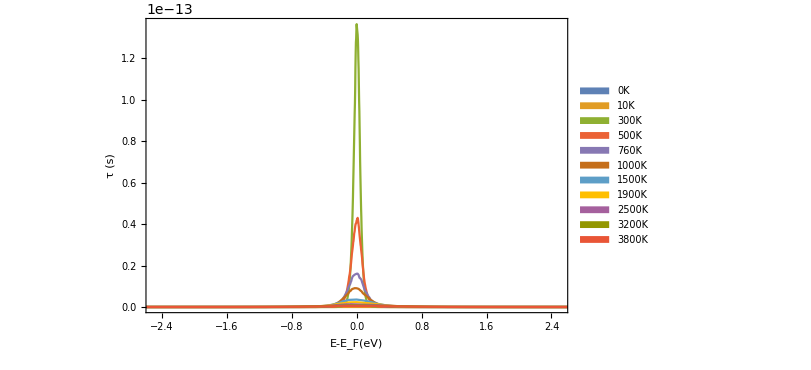

```mathematica
Plot[Evaluate@Table[Evaluate[sigmaK[x,tempps[[i]]]/interRate[[i]][x]],{i,1,11}],{x,-5,5},PlotLegends->SwatchLegend[temps],Frame->True,FrameLabel->{"E-E_F(eV)","τ (s)"},ImageSize->600,PlotRange->{{-2.5,2.5},All}]
```

```mathematica
Calculate average tau over 1 and over the kappa kernel;
```

```mathematica
tempps
```

{0,10,300,500,760,1000,1500,1900,2500,3200,3800}

```mathematica
upper=5;lower=-5;
Off[s::NIntegrate::slwcon]
Off[s::General::stop]
Off[s::NIntegrate::eincr]
Off[s::General::stop]
meanTau=Table[(1/NIntegrate[1,{energy,-5,5}])*NIntegrate[interTau[[i]][energy],{energy,lower,upper},MaxRecursion->50,PrecisionGoal->20],{i,2,11}]
(*Note delta_T=1 added to the integral over f' to make it stable*)
meanTauFD=Table[(1/NIntegrate[sigmaK[energy,tempps[[i]]],{energy,-5,5}])*NIntegrate[interTau[[i]][energy]*sigmaK[energy,tempps[[i]]],{energy,lower,upper},MaxRecursion->50,PrecisionGoal->20],{i,2,11}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.55408×10^-13 and 2.44361×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.8118×10^-14 and 1.10459×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.1584×10^-14 and 7.93452×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{1.55408×10^-14,7.8118×10^-15,5.1584×10^-15,3.44175×10^-15,2.64097×10^-15,1.73252×10^-15,1.36782×10^-15,1.01546×10^-15,7.70089×10^-16,9.13984×10^-16}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in energy near {energy} = {0.0193758}. NIntegrate obtained 0.500044 and 0.041055 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.06673×10^-13 and 1.55659×10^-29 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.31523×10^-14 and 4.84035×10^-22 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.99545×10^-15 and 2.97682×10^-21 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{4.1331×10^-13,1.31523×10^-14,6.99545×10^-15,4.15844×10^-15,3.10965×10^-15,1.9408×10^-15,1.48435×10^-15,1.05471×10^-15,7.58798×10^-16,5.64014×10^-16}

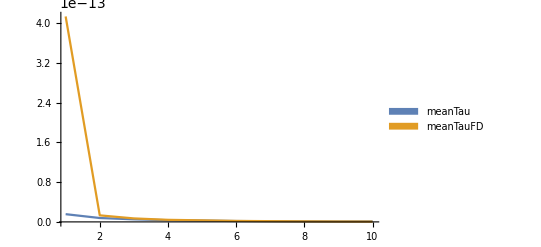

```mathematica
ListLinePlot[{meanTau,meanTauFD},PlotRange->All,PlotLegends->SwatchLegend[{"meanTau","meanTauFD"}]]
```

```mathematica
meanTauFD
```

{4.1331×10^-13,1.31523×10^-14,6.99545×10^-15,4.15844×10^-15,3.10965×10^-15,1.9408×10^-15,1.48435×10^-15,1.05471×10^-15,7.58798×10^-16,5.64014×10^-16}

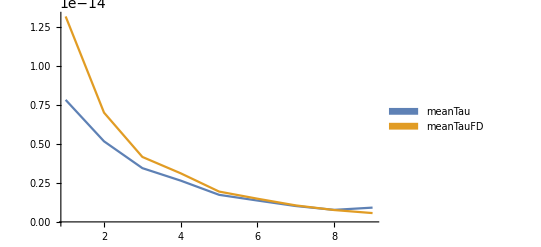

```mathematica
ListLinePlot[{meanTau[[2;;10]],meanTauFD[[2;;10]]},PlotRange->All,PlotLegends->SwatchLegend[{"meanTau","meanTauFD"}]]
```

```mathematica
temppps
```

{10,300,500,760,1000,1500,1900,2500,3200,3800}

```mathematica
tmean55tau=Transpose[{temppps[[2;;10]],meanTau[[2;;10]]}];
tmean55tauFD=Transpose[{temppps[[2;;10]],meanTauFD[[2;;10]]}];
(*Interpolation*)
tmean55tauinter=Interpolation[tmean55tau,InterpolationOrder->2];
tmean55tauFDinter=Interpolation[tmean55tauFD,InterpolationOrder->2];
```

```mathematica
Plot average tau over 1;
```

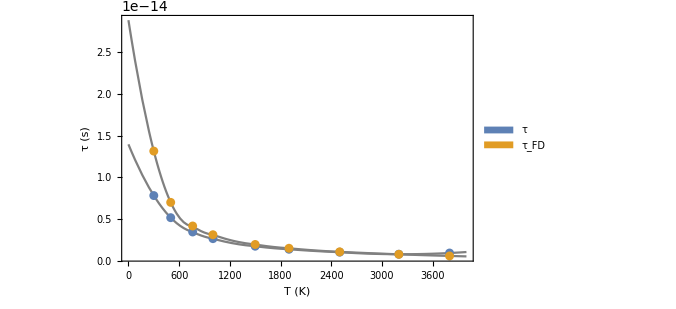

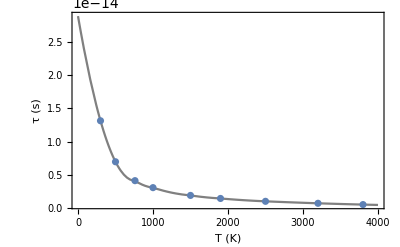

```mathematica
Show[Plot[Evaluate[{tmean55tauinter[x],tmean55tauFDinter[x]}],{x,0,4000},PlotRange->{{0,4000},All},PlotStyle->Gray,Frame->True,FrameLabel->{"T (K)","τ (s)"},ImageSize->500],ListPlot[{tmean55tau,tmean55tauFD},PlotLegends->SwatchLegend[{"τ","τ_FD"}]]]
Show[Plot[Evaluate[{tmean55tauFDinter[x]}],{x,0,4000},PlotRange->{{0,4000},All},PlotTheme->"Scientific",PlotStyle->Gray,Frame->True,FrameLabel->{Style["T (K)",15],Style["τ (s)",15]},FrameTicksStyle->15,ImageSize->400],ListPlot[{tmean55tauFD}]]
```

```mathematica
Import DOS;
```

```mathematica
(*Mermin+QHA*)
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/Conductivity_ZrC/OUT_ZrC_Mermin_QHA_PERF_KP191919"];
filesDOSperfMermin={"4667_000_000.hte.transdos", "4667_000_026.hte.transdos", "4671_300_026.hte.transdos", "4685_760_065.hte.transdos", "4731_1900_164.hte.transdos", "4760_2500_215.hte.transdos", "4802_3200_276.hte.transdos", "4848_3800_327.hte.transdos"};
(*Exclude the DOS with zero smearing*)
importedDOSperfMermin=Table[ReadList[filesDOSperfMermin[[i]],{Word,Word,Word}],{i,2,8}];
(*QHA*)
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/Conductivity_ZrC/OUT_ZrC_QHA_fixedTel_PERF_KP191919"];
filesDOSperf={"46583_SP_COND_252525.hte.transdos", "4685_SP_COND_252525.hte.transdos", "4730_SP_COND_252525.hte.transdos", "4759_SP_COND_252525.hte.transdos", "4801_SP_COND_252525.hte.transdos", "4850_SP_COND_252525.hte.transdos"};
importedDOSperf=Table[ReadList[filesDOSperf[[i]],{Word,Word,Word}],{i,1,6}];
```

```mathematica
Parse DOS;
```

```mathematica
(*Mermin+QHA*)
perfDOSM=Table[Transpose@{Table[ryd2eV*Internal`StringToDouble[importedDOSperfMermin[[j]][[i]][[1]]],{i,1,importedDOSperfMermin[[j]]//Length}],Table[eV2ryd*Internal`StringToDouble[importedDOSperfMermin[[j]][[i]][[2]]],{i,1,importedDOSperfMermin[[j]]//Length}]},{j,1,7}];
perfDOSintM=Table[Transpose@{Table[ryd2eV*Internal`StringToDouble[importedDOSperfMermin[[j]][[i]][[1]]],{i,1,importedDOSperfMermin[[j]]//Length}],Table[eV2ryd*Internal`StringToDouble[importedDOSperfMermin[[j]][[i]][[3]]],{i,1,importedDOSperfMermin[[j]]//Length}]},{j,1,7}];
(*QHA*)
perfDOS=Table[Transpose@{Table[ryd2eV*Internal`StringToDouble[importedDOSperf[[j]][[i]][[1]]],{i,1,importedDOSperf[[j]]//Length}],Table[eV2ryd*Internal`StringToDouble[importedDOSperf[[j]][[i]][[2]]],{i,1,importedDOSperf[[j]]//Length}]},{j,1,6}];
perfDOSint=Table[Transpose@{Table[ryd2eV*Internal`StringToDouble[importedDOSperf[[j]][[i]][[1]]],{i,1,importedDOSperf[[j]]//Length}],Table[eV2ryd*Internal`StringToDouble[importedDOSperf[[j]][[i]][[3]]],{i,1,importedDOSperf[[j]]//Length}]},{j,1,6}];
```

```mathematica
Plot DOS;
```

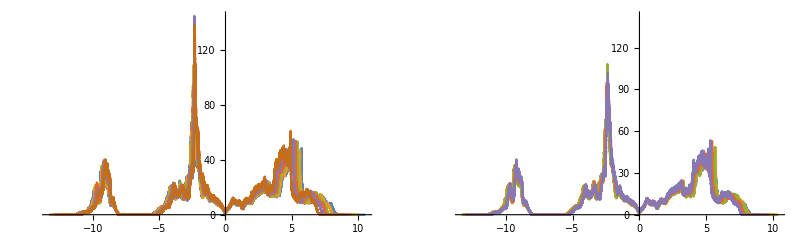

```mathematica
(*Increasing the smearing has very little effect on the band relaxation*)
GraphicsGrid[{{ListLinePlot[perfDOS,PlotRange->All],ListLinePlot[perfDOSM,PlotRange->All]}}]
```

```mathematica
Extract a window for moving averages of DOS;
```

```mathematica
(*To get an electronic DOS function, do moving average over some window, then interpolate cubic hermite polynomila*)
(*Let the smearing window be determined by the electronic temperature*)
smearingeV[window_]:=(window/(perfDOSM[[1]]//Length))*(-perfDOSM[[1]][[1]][[1]]+perfDOSM[[1]][[-1]][[1]])
windoweV[smearing_]:=(perfDOSM[[1]]//Length)*smearing/(-perfDOSM[[1]][[1]][[1]]+perfDOSM[[1]][[-1]][[1]])
smearingK[window_]:=(window/(perfDOSM[[1]]//Length))*(-perfDOSM[[1]][[1]][[1]]+perfDOSM[[1]][[-1]][[1]])/K2eV
windowK[smearing_]:=(perfDOSM[[1]]//Length)*smearing/(-perfDOSM[[1]][[1]][[1]]+perfDOSM[[1]][[-1]][[1]])*K2eV
windoweV[0.026];
windowK[300];
windows=Table[windowK[temps2[[i]]],{i,1,7}]
Floor@windows
(*IMPORTANT - double check the temperature and volumes correspond to plain QHA - mermin-QHA should be fine*)
```

{19.002,19.002,48.1383,120.346,158.35,202.688,240.691}

{19,19,48,120,158,202,240}

```mathematica
Interpolate moving averaged DOS;
```

```mathematica
(*Check moving average over different windows - 50 is fine*)
inter1=Interpolation[MovingAverage[perfDOSM[[1]],1],Method->"Hermite",InterpolationOrder->3];
inter5=Interpolation[MovingAverage[perfDOSM[[1]],5],Method->"Hermite",InterpolationOrder->3];
inter10=Interpolation[MovingAverage[perfDOSM[[1]],10],Method->"Hermite",InterpolationOrder->3];
inter50=Interpolation[MovingAverage[perfDOSM[[1]],50],Method->"Hermite",InterpolationOrder->3];
inter100=Interpolation[MovingAverage[perfDOSM[[1]],100],Method->"Hermite",InterpolationOrder->3];
```

```mathematica
interFixed=Table[Interpolation[MovingAverage[perfDOSM[[i]],Floor@windows[[1]]],Method->"Hermite",InterpolationOrder->3],{i,1,7}];
interMoving=Table[Interpolation[MovingAverage[perfDOSM[[i]],Floor@windows[[i]]],Method->"Hermite",InterpolationOrder->3],{i,1,7}];
```

```mathematica
Plot interpolated moving averaged DOS;
```

```mathematica
GraphicsGrid[{{Plot[Evaluate@Table[interMoving[[i]][x]+i,{i,1,7}],{x,-5,5},PlotRange->All,PlotLegends->SwatchLegend[Table[temps2[[i]],{i,1,7}]],ImageSize->450],Plot[Evaluate@Table[interFixed[[i]][x]+i,{i,1,7}],{x,-5,5},PlotRange->All,PlotLegends->SwatchLegend[Table[temps2[[i]],{i,1,7}]],ImageSize->450]}},ImageSize->1020]
```

-Graphics-

#### Import conductivity;

```mathematica
(*Mermin+QHA*)
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/Conductivity_ZrC/OUT_ZrC_Mermin_QHA_PERF_KP191919"];
filesTRACEperfMermin={"4667_000_000.hte.trace", "4667_000_026.hte.trace", "4671_300_026.hte.trace", "4685_760_065.hte.trace", "4731_1900_164.hte.trace", "4760_2500_215.hte.trace", "4802_3200_276.hte.trace", "4848_3800_327.hte.trace"};
(*Exclude the DOS with zero smearing*)
importedTRACEperfMermin=Table[ReadList[filesTRACEperfMermin[[i]],{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}],{i,2,8}];
(*QHA*)
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/Conductivity_ZrC/OUT_ZrC_QHA_fixedTel_PERF_KP191919"];
filesTRACEperf={"46583_SP_COND_252525.hte.trace", "4685_SP_COND_252525.hte.trace", "4730_SP_COND_252525.hte.trace", "4759_SP_COND_252525.hte.trace", "4801_SP_COND_252525.hte.trace", "4850_SP_COND_252525.hte.trace"};
importedTRACEperf=Table[ReadList[filesTRACEperf[[i]],{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}],{i,1,6}];
```

```mathematica
Parse conductivity;
```

```mathematica
(*# Ef[Ry] T[K] N DOS(Ef) S s/t R_H kappa0 c chi*)
(*Mermin+QHA*)
perfSIGMAMoTau=Table[Table[{importedTRACEperfMermin[[k]][[i]][[2]],importedTRACEperfMermin[[k]][[i]][[6]]},{i,1,importedTRACEperfMermin[[k]]//Length}][[1;;100]],{k,1,7}];
perfKAPPAMoTau=Table[Table[{importedTRACEperfMermin[[k]][[i]][[2]],importedTRACEperfMermin[[k]][[i]][[8]]},{i,1,importedTRACEperfMermin[[k]]//Length}][[1;;100]],{k,1,7}];
```

```mathematica
perfSIGMAoTau=Table[Table[{importedTRACEperf[[k]][[i]][[2]],importedTRACEperf[[k]][[i]][[6]]},{i,1,importedTRACEperf[[k]]//Length}][[1;;100]],{k,1,6}];
perfKAPPAoTau=Table[Table[{importedTRACEperf[[k]][[i]][[2]],importedTRACEperf[[k]][[i]][[8]]},{i,1,importedTRACEperf[[k]]//Length}][[1;;100]],{k,1,6}];
```

```mathematica
ListPlot[{perfSIGMAMoTau[[1]],perfSIGMAMoTau[[7]]}]
ListPlot[{perfSIGMAoTau[[1]],perfSIGMAoTau[[6]]}]
```

-Graphics-

-Graphics-

```mathematica
ListPlot[{perfSIGMAMoTau[[6]],perfSIGMAoTau[[6]]}]
ListPlot[{perfKAPPAMoTau[[6]],perfKAPPAoTau[[6]]}]
```

-Graphics-

-Graphics-

```mathematica
interSIGMAMoTau=Table[Interpolation[perfSIGMAMoTau[[i]]],{i,1,7}];
interKAPPAMoTau=Table[Interpolation[perfKAPPAMoTau[[i]]],{i,1,7}];
interSIGMAoTau=Table[Interpolation[perfSIGMAoTau[[i]]],{i,1,6}];
interKAPPAoTau=Table[Interpolation[perfKAPPAoTau[[i]]],{i,1,6}];
```

```mathematica
GraphicsGrid[{{Plot[Evaluate@Table[interSIGMAMoTau[[i]][t],{i,1,6}],{t,100,1500},ImageSize->400,PlotLegends->SwatchLegend[Table[temps3[[i]],{i,1,6}]]],Plot[Evaluate@Table[interSIGMAoTau[[i]][t],{i,1,6}],{t,100,1500},ImageSize->400,PlotLegends->SwatchLegend[Table[temps3[[i]],{i,1,6}]]]}},ImageSize->1000];
GraphicsGrid[{{Plot[Evaluate@Table[interKAPPAoTau[[i]][t],{i,1,6}],{t,100,1500},ImageSize->400,PlotLegends->SwatchLegend[Table[temps3[[i]],{i,1,6}]]],Plot[Evaluate@Table[interKAPPAoTau[[i]][t],{i,1,6}],{t,100,1500},ImageSize->400,PlotLegends->SwatchLegend[Table[temps3[[i]],{i,1,6}]]]}},ImageSize->1000];
```

```mathematica
(*Make sigma including tau*)
(*tmean55tauinter=Interpolation[tmean55tau,InterpolationOrder->6];
tmean55tauFDinter=Interpolation[tmean55tauFD,InterpolationOrder->6];*)
interSIGMAM=Table[interSIGMAMoTau[[i]][t]*tmean55tauinter[t],{i,1,6}];
interSIGMAMFD=Table[interSIGMAMoTau[[i]][t]*tmean55tauFDinter[t],{i,1,6}];
interSIGMAMfixTau300=Table[interSIGMAMoTau[[i]][t]*tmean55tauinter[300],{i,1,6}];
(*Make kappa including tau*)
interKAPPAM=Table[interKAPPAMoTau[[i]][t]*tmean55tauinter[t],{i,1,6}];
interKAPPAMFD=Table[interKAPPAMoTau[[i]][t]*tmean55tauFDinter[t],{i,1,6}];
interKAPPAMfixTau300=Table[interKAPPAMoTau[[i]][t]*tmean55tauinter[300],{i,1,6}];
```

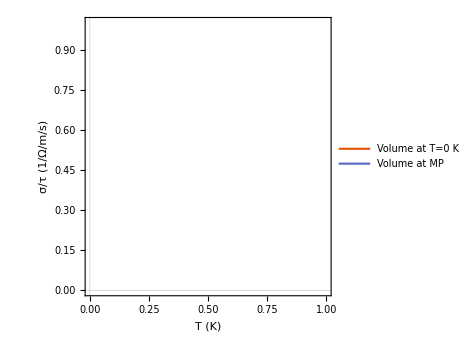

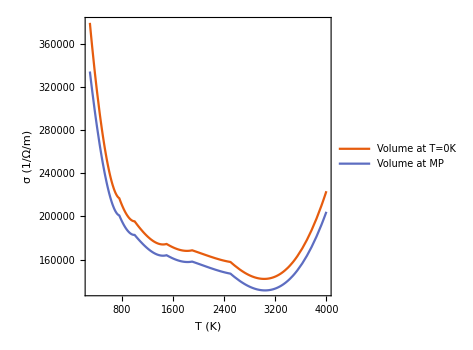

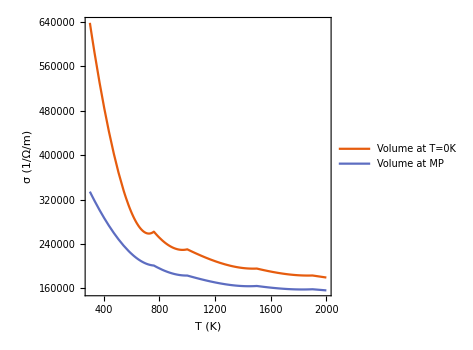

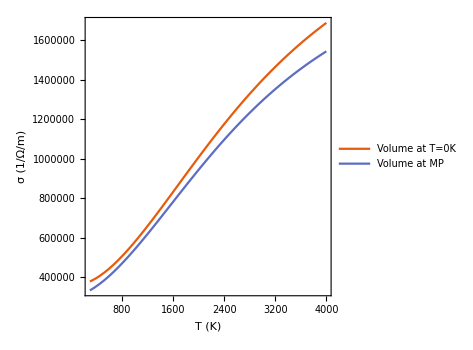

```mathematica
Plot[Evaluate@Table[interSIGMAMoTau[[i]][t],{i,1,6,5}],{t,100,1500},ImageSize->350,AspectRatio->1,PlotTheme->"Scientific",Frame->True,FrameLabel->{Style["T (K)",15],Style["σ/τ  (1/Ω/m/s)",15]},FrameTicksStyle->15,PlotLegends->Placed[{Style["Volume at T=0 K",15],Style["Volume at MP",15]},{0.3,0.8}]]
Plot[{Evaluate@interSIGMAM[[1]],Evaluate@interSIGMAM[[6]]},{t,300,4000},PlotRange->All,ImageSize->350,AspectRatio->1,PlotTheme->"Scientific",Frame->True,FrameLabel->{Style["T (K)",15],Style["σ  (1/Ω/m)",15]},FrameTicksStyle->15,PlotLegends->Placed[{Style["Volume at T=0K",15],Style["Volume at MP",15]},{0.7,0.8}]]
Plot[{Evaluate@interSIGMAMFD[[1]],Evaluate@interSIGMAM[[6]]},{t,300,2000},PlotRange->All,ImageSize->350,AspectRatio->1,PlotTheme->"Scientific",Frame->True,FrameLabel->{Style["T (K)",15],Style["σ  (1/Ω/m)",15]},FrameTicksStyle->15,PlotLegends->Placed[{Style["Volume at T=0K",15],Style["Volume at MP",15]},{0.7,0.8}]]
Plot[{Evaluate@interSIGMAMfixTau300[[1]],Evaluate@interSIGMAMfixTau300[[6]]},{t,300,4000},PlotRange->All,ImageSize->350,AspectRatio->1,PlotTheme->"Scientific",Frame->True,FrameLabel->{Style["T (K)",15],Style["σ  (1/Ω/m)",15]},FrameTicksStyle->15,PlotLegends->Placed[{Style["Volume at T=0K",15],Style["Volume at MP",15]},{0.3,0.8}]]
```

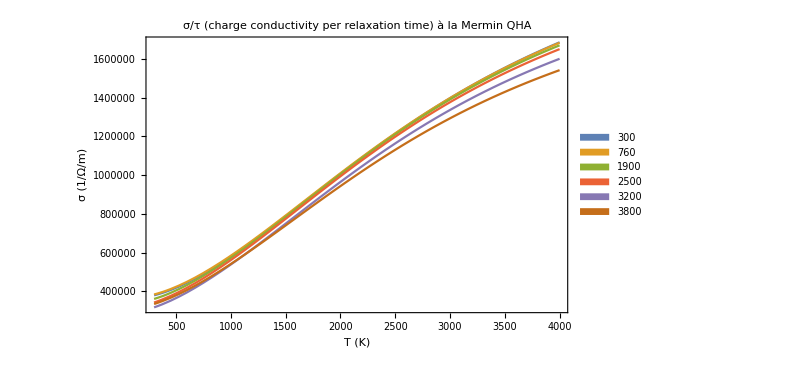

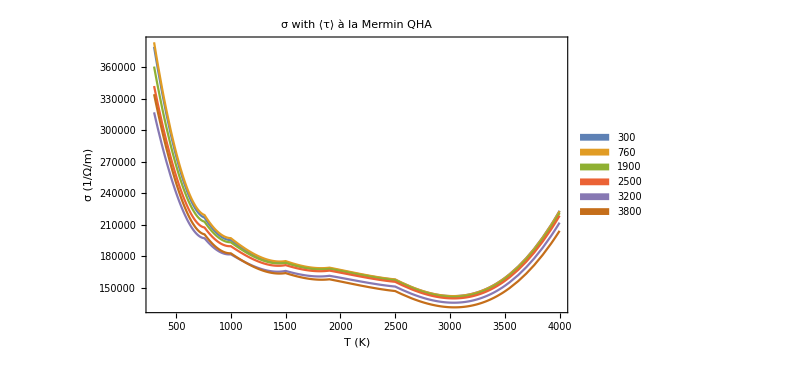

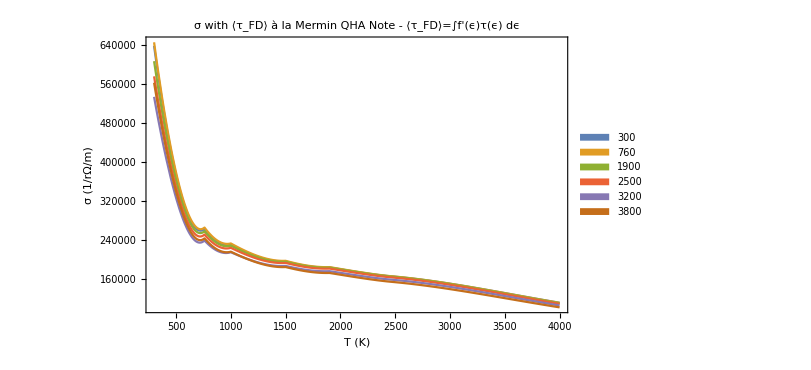

```mathematica
Plot[Evaluate@interSIGMAMfixTau300,{t,300,4000},PlotRange->All,PlotLegends->SwatchLegend[temps3],Frame->True,FrameLabel->{"T (K)","σ (1/Ω/m)"},ImageSize->600,PlotLabel->"σ/τ (charge conductivity per relaxation time) à la Mermin QHA"]
Plot[Evaluate@interSIGMAM,{t,300,4000},PlotRange->All,PlotLegends->SwatchLegend[temps3],Frame->True,FrameLabel->{"T (K)","σ (1/Ω/m)"},ImageSize->600,PlotLabel->"σ with ⟨τ⟩ à la Mermin QHA"]
Plot[Evaluate@interSIGMAMFD,{t,300,4000},PlotRange->All,PlotLegends->SwatchLegend[temps3],Frame->True,FrameLabel->{"T (K)","σ (1/rΩ/m)"},ImageSize->600,PlotLabel->"σ with ⟨τ_FD⟩ à la Mermin QHA \n Note - ⟨τ_FD⟩=∫f'(ϵ)τ(ϵ) dϵ"]
```

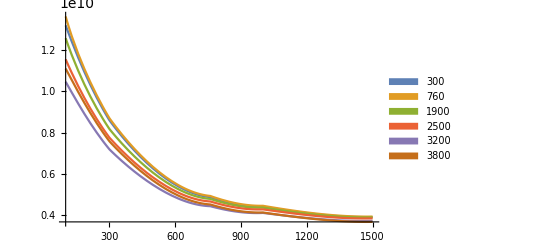

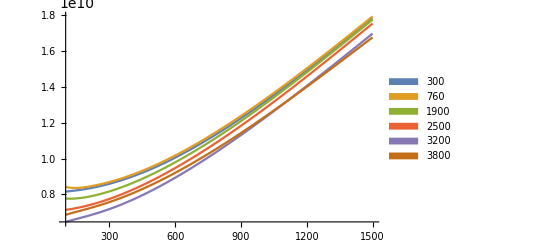

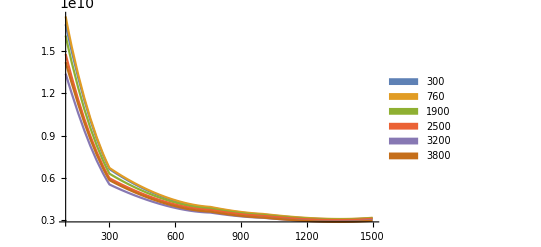

```mathematica
Plot[Evaluate@interSIGMAM,{t,100,1500},PlotRange->All,PlotLegends->SwatchLegend[temps3]]
Plot[Evaluate@interSIGMAMfixTau300,{t,100,1500},PlotRange->All,PlotLegends->SwatchLegend[temps3]]
Plot[Evaluate@interSIGMAMFD,{t,100,1500},PlotRange->All,PlotLegends->SwatchLegend[temps3]]
```

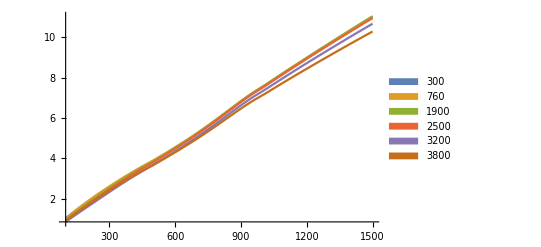

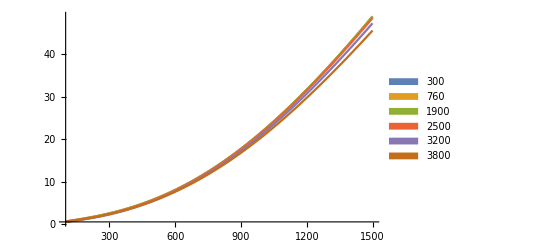

```mathematica
Plot[Evaluate@interKAPPAM,{t,100,1500},PlotRange->All,PlotLegends->SwatchLegend[temps3]]
Plot[Evaluate@interKAPPAMfixTau300,{t,100,1500},PlotRange->All,PlotLegends->SwatchLegend[temps3]]
```

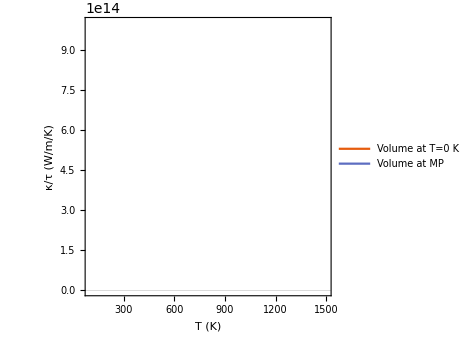

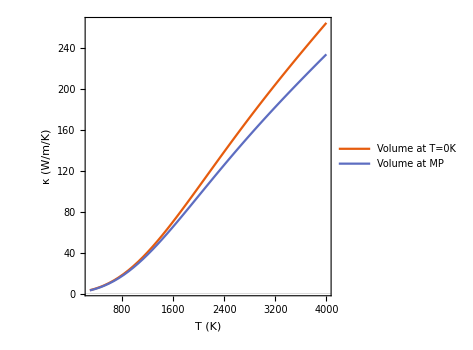

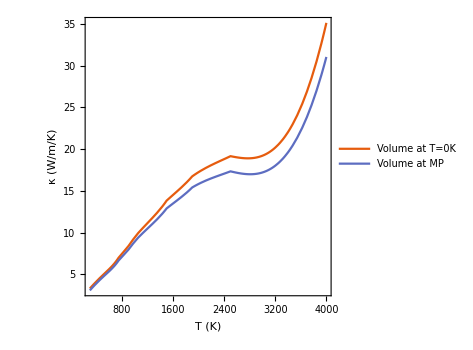

```mathematica
Plot[Evaluate@Table[interKAPPAMoTau[[i]][t],{i,1,6,5}],{t,100,1500},ImageSize->350,AspectRatio->1,PlotTheme->"Scientific",Frame->True,FrameLabel->{Style["T (K)",15],Style["κ/τ  (W/m/K)",15]},FrameTicksStyle->15,PlotLegends->Placed[{Style["Volume at T=0 K",15],Style["Volume at MP",15]},{0.3,0.8}]]
Plot[{Evaluate@interKAPPAMfixTau300[[1]],Evaluate@interKAPPAMfixTau300[[6]]},{t,300,4000},PlotRange->All,ImageSize->350,AspectRatio->1,PlotTheme->"Scientific",Frame->True,FrameLabel->{Style["T (K)",15],Style["κ  (W/m/K)",15]},FrameTicksStyle->15,PlotLegends->Placed[{Style["Volume at T=0K",15],Style["Volume at MP",15]},{0.3,0.8}]]
Plot[{Evaluate@interKAPPAM[[1]],Evaluate@interKAPPAM[[6]]},{t,300,4000},PlotRange->All,ImageSize->350,AspectRatio->1,PlotTheme->"Scientific",Frame->True,FrameLabel->{Style["T (K)",15],Style["κ  (W/m/K)",15]},FrameTicksStyle->15,PlotLegends->Placed[{Style["Volume at T=0K",15],Style["Volume at MP",15]},{0.7,0.2}]]
```

```mathematica
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/Conductivity_ZrC/OUT_ZrC_Mermin_QHA_PERF_KP191919/"];
filev2dos={"4667_000_000.hte.v2dos", "4667_000_026.hte.v2dos", "4671_300_026.hte.v2dos", "4685_760_065.hte.v2dos", "4731_1900_164.hte.v2dos", "4760_2500_215.hte.v2dos", "4802_3200_276.hte.v2dos", "4848_3800_327.hte.v2dos"};
zrcv2dos=Table[ReadList[filev2dos[[i]],{Number, Number,Number, Number,Number, Number,Number, Number,Number, Number}],{i,2,filev2dos//Length}];
```

```mathematica
v2dosRy=Table[Transpose[{Transpose[zrcv2dos[[i]]][[1]],Transpose[zrcv2dos[[i]]][[2]]}],{i,1,7,1}];
v2dos1=Table[Transpose[{ryd2eV*Transpose[zrcv2dos[[i]]][[1]],Transpose[zrcv2dos[[i]]][[2]]}],{i,1,7,1}];
v2dosNorm=Table[Table[{ryd2eV*zrcv2dos[[j]][[i]][[1]],Norm[zrcv2dos[[j]][[i]][[2;;10]]]},{i,1,zrcv2dos[[j]]//Length}],{j,1,7}];
v2dosNormD=Table[Table[{ryd2eV*zrcv2dos[[j]][[i]][[1]],Norm[zrcv2dos[[j]][[i]][[2;;10;;4]]]},{i,1,zrcv2dos[[j]]//Length}],{j,1,7}];
v2dosNormInter=Table[Interpolation[MovingAverage[v2dosNormD[[i]],50]][x],{i,1,7}];
```

```mathematica
(*Doing a moving average, with window set to temperature*)
windowKv2[smearing_]:=(v2dosNorm[[1]]//Length)*smearing/(-v2dosNorm[[1]][[1]][[1]]+v2dosNorm[[1]][[-1]][[1]])*K2eV
windowsv2=Table[windowKv2[temps2[[i]]],{i,1,7}];
v2interMoving=Table[Interpolation[MovingAverage[v2dosNorm[[i]],Floor@windows[[i]]],Method->"Hermite",InterpolationOrder->3],{i,1,7}];
```

```mathematica
Show[{Table[ListPlot[v2dosNorm[[i]],PlotStyle->Directive[Orange,Opacity[0.25]],PlotRange->{{-5.5,5.5},All}],{i,1,7}],
Plot[Evaluate@Table[v2interMoving[[i]][x],{i,1,7}],{x,-6,6},PlotRange->{{-5.5,5.5},All}]},ImageSize->800]
```

-Graphics-

```mathematica
(*DOS interpolated*)
Plot[{interMoving[[2]][x]},{x,-5.5,5.5},PlotRange->All]
(*v2/dos interpolated*)
Plot[{v2interMoving[[2]][x]},{x,-5.5,5.5},PlotRange->All]
(*v2=v2/dos*dos interpolated*)
Plot[v2interMoving[[2]][x]*interMoving[[2]][x],{x,-5.5,5.5},PlotRange->All]
Plot[v2interMoving[[2]][x]/interMoving[[2]][x],{x,-5,5},PlotRange->All]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
(*Tau averaged over FD*v2dos*)
```

```mathematica
temps4
```

{300,760,1900,2500,3200,3800}

```mathematica
tempps
```

{0,10,300,500,760,1000,1500,1900,2500,3200,3800}

```mathematica
(*Get intertau at 300 760 1900 2500 3200 3800*)
interTau4={interTau[[2]][x],interTau[[3]][x],interTau[[5]][x],interTau[[8]][x],interTau[[9]][x],interTau[[10]][x],interTau[[11]][x]}
```

{InterpolatingFunction[{{-5.41015, 5.75599}}, <>][x],InterpolatingFunction[{{-5.38765, 5.74398}}, <>][x],InterpolatingFunction[{{-5.34366, 5.68638}}, <>][x],InterpolatingFunction[{{-5.23793, 5.47322}}, <>][x],InterpolatingFunction[{{-5.1603, 5.34741}}, <>][x],InterpolatingFunction[{{-5.08223, 5.14403}}, <>][x],InterpolatingFunction[{{-4.93893, 4.97902}}, <>][x]}

```mathematica
Plot[{v2interMoving[[1]][x],v2interMoving[[2]][x]},{x,-5,5}]
Plot[{interMoving[[1]][x],interMoving[[2]][x]},{x,-5,5}]
Plot[{interTau4[[1]],interTau4[[2]]},{x,-5,5}]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
Plot[Evaluate@Table[Evaluate[sigmaK[x,temps4[[i]]]*interTau4[[i]]*(v2interMoving[[i]][x]*interMoving[[i]][x])],{i,1,7}],{x,-5,5},PlotLegends->SwatchLegend[temps4],Frame->True,FrameLabel->{"E-E_F(eV)","1/τ (s)"},ImageSize->600,PlotRange->{{-2.5,2.5},All}]
```

-Graphics-

```mathematica
mean55tauFDv2=Table[(1/NIntegrate[sigmaK[energy,temps4[[i]]]*(v2interMoving[[i]][energy]*interMoving[[i]][energy]),{energy,-5,5}])*NIntegrate[(interTau4[[i]]/.x->energy)*sigmaK[energy,temps4[[i]]]*(v2interMoving[[i]][energy]*interMoving[[i]][energy]),{energy,-5,5},MaxRecursion->50,PrecisionGoal->20],{i,1,7}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in energy near {energy} = {0.0193758}. NIntegrate obtained 0.0870923 and 0.00703979 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.63588×10^-14 and 1.78473×10^-28 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in energy near {energy} = {-0.000155416}. NIntegrate obtained 0.194883 and 0.00054023 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.53211×10^-15 and 3.1265×10^-22 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in energy near {energy} = {-0.0392179}. NIntegrate obtained 0.253266 and 0.000229337 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.03869×10^-15 and 3.24021×10^-21 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{4.17474×10^-13,1.2993×10^-14,4.10119×10^-15,1.43981×10^-15,1.01447×10^-15,7.28532×10^-16,5.41363×10^-16}

```mathematica
tmean55tauFDv2=Transpose[{temps4,mean55tauFDv2}];
(*Interpolation*)
tmean55tauFDv2inter=Interpolation[tmean55tauFDv2,InterpolationOrder->1];
```

```mathematica
ListPlot@tmean55tauFDv2
```

-Graphics-

```mathematica
Plot[tmean55tauFDv2inter[x],{x,1,4000},PlotRange->All]
```

-Graphics-

```mathematica
Show[Plot[Evaluate[{tmean55tauFDv2inter[x]}],{x,0,4000},PlotRange->{{0,4000},All},PlotTheme->"Scientific",PlotStyle->Gray,Frame->True,FrameLabel->{Style["T (K)",15],Style["1/τ (1/s)",15]},FrameTicksStyle->15,ImageSize->400],ListPlot[{tmean55tauFDv2}]]
```

-Graphics-

```mathematica
(*Make sigma including tau*)
interSIGMAMFDv2=Table[interSIGMAMoTau[[i]][t]*tmean55tauFDinter[t],{i,1,6}];
(*Make kappa including tau*)
interKAPPAMFDv2=Table[interKAPPAMoTau[[i]][t]*tmean55tauFDinter[t],{i,1,6}];
```

```mathematica
temps4
```

{10,300,760,1900,2500,3200,3800}

```mathematica
ListPlot@Transpose[Table[Table[{temps4[[j]],1/(interKAPPAMoTau[[i]][temps4[[j]]]*tmean55tauFDinter[temps4[[j]]])},{i,1,6}],{j,1,7}]][[6]]
```

-Graphics-

```mathematica
Plot[{Evaluate@interKAPPAMFDv2[[1]],Evaluate@interKAPPAMFDv2[[6]]},{t,100,3500},PlotRange->All,ImageSize->350,AspectRatio->1,PlotTheme->"Scientific",Frame->True,FrameLabel->{Style["T (K)",15],Style["κ  (W/m/K)",15]},FrameTicksStyle->15,PlotLegends->Placed[{Style["Volume at T=0K",15],Style["Volume at MP",15]},{0.7,0.2}]]
```

-Graphics-

```mathematica
Plot[{Evaluate@interSIGMAMFDv2[[1]],Evaluate@interSIGMAMFDv2[[6]]},{t,300,3000},PlotRange->All,ImageSize->350,AspectRatio->1,PlotTheme->"Scientific",Frame->True,FrameLabel->{Style["T (K)",15],Style["σ  (1/Ω/m)",15]},FrameTicksStyle->15,PlotLegends->Placed[{Style["Volume at T=0K",15],Style["Volume at MP",15]},{0.7,0.8}]]
```

-Graphics-